```mathematica
(* This cell contains generic setup stuff to prepare for execution of the programs *)
ClearAll["Global`*"]; ParamsAreSet = False;
If[$VersionNumber < 6,(*then*) Print["These programs require Mathematica version 6 or greater."]; Abort[]];
(* If running from Notebook front end, set directory to Notebook's directory *)
If[Length[$FrontEnd] > 0, NBDir = SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
If[Length[$FrontEnd] == 0,SetDirectory["/Volumes/Data/Work/BufferStock/Endo/Latest/Code/Mathematica/Results/Endo"]];
SaveFigs = False;
HomeDir = Directory[];
CodeDir = HomeDir<>"/../../CoreCode";
CDToHomeDir := SetDirectory[HomeDir];
CDToCodeDir := SetDirectory[HomeDir<>"/../../CoreCode"];

CDToCodeDir;
<<SetupModelSolutionRoutines.m;
<<SetParamsToBaselineVals.m;
PermGridLength = TranGridLengthSetup = 1;
℘ = 0.00000000001; ℘Cancel = 1 - ℘; SetupShocks;
aLargeMax = 10 ℏInf; (* Large number defines the maximum gridpoint for a *)
aSmallMax = 3;  (* Small number defines the gridpoint below which aGridVecExcBot will be dense *)ConstructLastPeriodToConsumeEverything;
aGridVecExcBotSmallLength = 10000;
aGridVecExcBotLargeLength = 100;
TimesToNestSmallGrid = 100;(*IntegerPart[Abs[100 Log[℘]]];*)
SetupGrids;
Do[SolveAnotherPeriod,{5}];
```

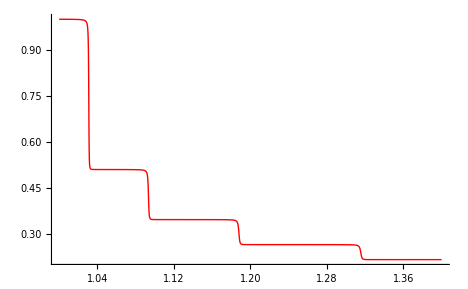

```mathematica
κNumerical=Plot[κ[m],{m,1,1.4},PlotRange->All,PlotStyle->Red]
```

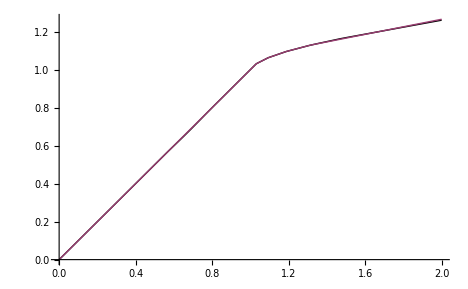

```mathematica
c♯3PeriodsData=Join[{{0.,0.}},Map[{m♯[#],c♯[#]}&,{1,2,3,4,6}]];c♯3PeriodsFunc=Interpolation[c♯3PeriodsData,InterpolationOrder->1];
Plot[{𝒸[m],c♯3PeriodsFunc[m]},{m,0,2}]
```

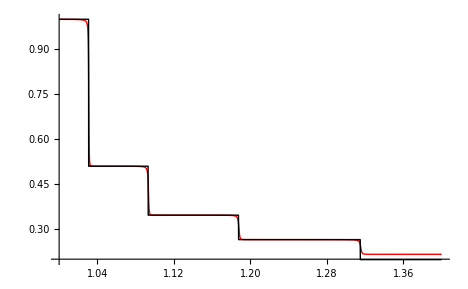

```mathematica
κExact=Plot[c♯3PeriodsFunc'[m],{m,1,1.4}];
Show[κNumerical,κExact]
```